```mathematica
data=Import["C:\\Users\\lwang\\OneDrive\\Documents\\Datas\\Clusters\\GC\\ntime.dat","Table"];
```

```mathematica
rdat={data[[1]]};
tcount=0;
Do[If[data[[i-1,1]]=="PE",AppendTo[rdat,Prepend[data[[i]],tcount]],If[data[[i,1]]≠ "PE",AppendTo[rdat,{tcount}~Join~data[[i,1;;2]]~Join~(data[[i,3;;]]-data[[i-1,3;;]])]]];tcount=tcount+1,{i,2,Length@data}]
```

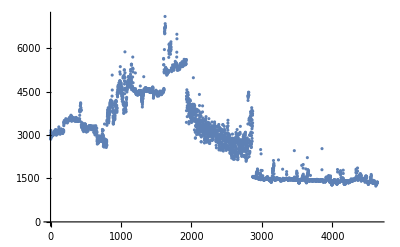

```mathematica
ListPlot[rdat[[All,{1,4}]]]
```

```mathematica
Export["C:\\Users\\lwang\\OneDrive\\Documents\\Datas\\NBPrf\\timeevolve.txt",rdat]
```

C:\Users\lwang\OneDrive\Documents\Datas\NBPrf\timeevolve.txt